# Scara Robot Kinematic Analysis : manipulability ellipsoids

## Rotation matrices

```mathematica
ClearAll["Global`*"]
```

-Graphics--Graphics-

Position analysis: direct kinematics

```mathematica
Mrotztrasl[α_,point_]:={{Cos@α, -Sin@α, 0, point[[1]]}, {Sin@α, Cos@α, 0, point[[2]]}, {0, 0, 1, point[[3]]}, {0, 0, 0, 1}}
```

```mathematica
A={L1 Cos[θ1],L1 Sin[θ1],h,1};
```

```mathematica
M01=Mrotztrasl[θ1,A];M01//MatrixForm
```

(Cos[θ1] | -Sin[θ1] | 0 | L1 Cos[θ1]
Sin[θ1] | Cos[θ1] | 0 | L1 Sin[θ1]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
P1={L2 Cos[θ2],L2 Sin[θ2],0,1};
```

```mathematica
P=M01.P1//Simplify;
```

```mathematica
M12=Mrotztrasl[θ2,P1];M12//MatrixForm
```

(Cos[θ2] | -Sin[θ2] | 0 | L2 Cos[θ2]
Sin[θ2] | Cos[θ2] | 0 | L2 Sin[θ2]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=M01.M12//Simplify;M02//MatrixForm
```

(Cos[θ1+θ2] | -Sin[θ1+θ2] | 0 | L1 Cos[θ1]+L2 Cos[θ1+θ2]
Sin[θ1+θ2] | Cos[θ1+θ2] | 0 | L1 Sin[θ1]+L2 Sin[θ1+θ2]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
E2={0,0,-L,1};
```

```mathematica
M23=Mrotztrasl[0,E2];M23//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | -L
0 | 0 | 0 | 1)

```mathematica
M03=M02.M23;M03//MatrixForm
```

(Cos[θ1+θ2] | -Sin[θ1+θ2] | 0 | L1 Cos[θ1]+L2 Cos[θ1+θ2]
Sin[θ1+θ2] | Cos[θ1+θ2] | 0 | L1 Sin[θ1]+L2 Sin[θ1+θ2]
0 | 0 | 1 | h-L
0 | 0 | 0 | 1)

```mathematica
EE=M03.{0,0,0,1};EE//MatrixForm
```

(L1 Cos[θ1]+L2 Cos[θ1+θ2]
L1 Sin[θ1]+L2 Sin[θ1+θ2]
h-L
1)

Let us study the manipulability ellipsoids in the plane . We restrict point E to the first two components (EEc) and perform the analysis .

```mathematica
EEc={EE[[1]],EE[[2]]};EEc//MatrixForm
```

(L1 Cos[θ1]+L2 Cos[θ1+θ2]
L1 Sin[θ1]+L2 Sin[θ1+θ2])

```mathematica
Jac=D[EEc,{{θ1,θ2}}];Jac//MatrixForm
```

(-L1 Sin[θ1]-L2 Sin[θ1+θ2] | -L2 Sin[θ1+θ2]
L1 Cos[θ1]+L2 Cos[θ1+θ2] | L2 Cos[θ1+θ2])

```mathematica
DetJac=Det@Jac//Simplify
```

L1 L2 Sin[θ2]

### Singular configuration

```mathematica
TrigExpand[Sin[2x]] (*e.g.*)
```

2 Cos[x] Sin[x]

```mathematica
θ1Singular=Solve[TrigExpand[DetJac==0],θ1]//Simplify
```

{}

```mathematica
θ2Singular=Solve[TrigExpand[DetJac==0],θ2]//Simplify
```

{{θ2→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ2→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

## Force Ellipsoid

We take a reference robot configuration

```mathematica
data={L1->0.3,L2->0.3};
```

```mathematica
ref={θ1->π/6,θ2->π/3};
```

```mathematica
F={Fx,Fy};
```

Force ellipsoid: every point inside the force is the admissible force  that the robot can apply in that direction. The budget function is the norm of the joint forces

```mathematica
AF=Jac.Transpose[Jac]//Simplify;AF//MatrixForm
```

(L2^2 Sin[θ1+θ2]^2+(L1 Sin[θ1]+L2 Sin[θ1+θ2])^2 | -L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])
-L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2]) | L2^2 Cos[θ1+θ2]^2+(L1 Cos[θ1]+L2 Cos[θ1+θ2])^2)

```mathematica
Fellipse=Transpose@F.AF.F-Kf^2//Simplify(*Force ellipsoid equation*)
```

-Kf^2+Fy^2 L1^2 Cos[θ1]^2+2 Fy^2 L2^2 Cos[θ1+θ2]^2+Fx^2 L1^2 Sin[θ1]^2+2 Fy L1 Cos[θ1] (Fy L2 Cos[θ1+θ2]-Fx L1 Sin[θ1])+2 Fx^2 L1 L2 Sin[θ1] Sin[θ1+θ2]+2 Fx^2 L2^2 Sin[θ1+θ2]^2-2 Fx Fy L2^2 Sin[2 (θ1+θ2)]-2 Fx Fy L1 L2 Sin[2 θ1+θ2]

```mathematica
NumericalMatF=AF/.data/.ref;NumericalMatF//MatrixForm
```

(0.2925 | -0.116913
-0.116913 | 0.0675)

```mathematica
EigVecF=Eigenvectors@NumericalMatF;EigVecF//MatrixForm
EigValF=Eigenvalues@NumericalMatF
```

(-0.920156 | 0.391551
-0.391551 | -0.920156)

{0.34225,0.0177502}

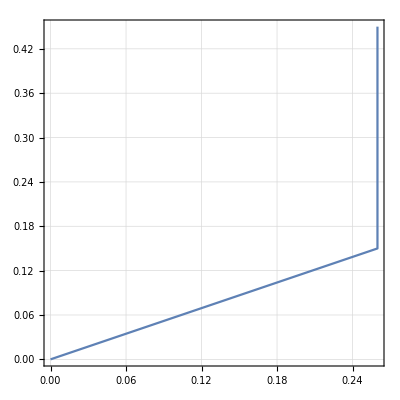

```mathematica
plScara=ListLinePlot[{{0,0},{A[[1]],A[[2]]},{EEc[[1]],EEc[[2]]}}/.data/.ref,Frame->True,AspectRatio->1,GridLines->Automatic]
```

```mathematica
point1={0,0};
```

```mathematica
point2=1/(√Re[EigValF[[1]]]){Re[EigVecF[[1,1]]],Re[EigVecF[[1,2]]]}
```

{-1.57286,0.669294}

```mathematica
plEigVecF1=ListLinePlot[{point1,point2},PlotStyle->Red];
```

```mathematica
point3=1/(√Re[EigValF[[2]]]){Re[EigVecF[[2,1]]],Re[EigVecF[[2,2]]]}
```

{-2.93892,-6.90653}

```mathematica
plEigVecF2=ListLinePlot[{point1,point3},PlotStyle->Green];
```

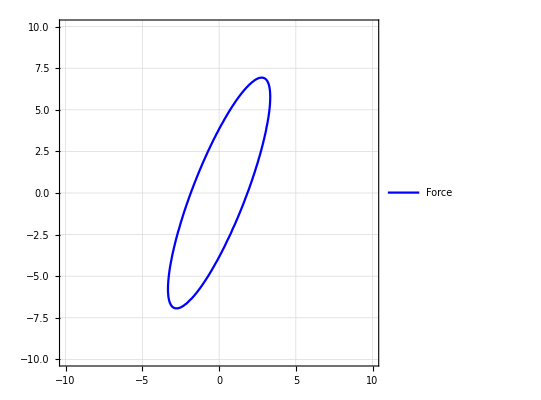

```mathematica
plContourF=ContourPlot[(Fellipse/.data/.ref/.Kf->1)==0,{Fx,-10,10},{Fy,-10,10},GridLines->Automatic,ContourStyle->Blue,PlotLegends->LineLegend[{Blue},{"Force"}]]
```

### Force Ellipsoid

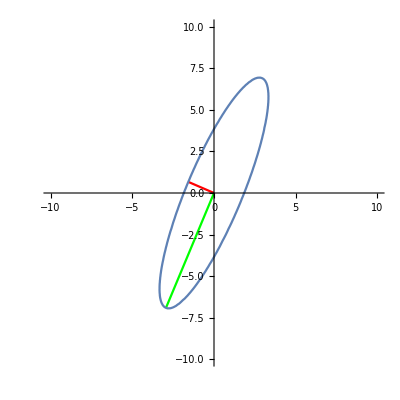

```mathematica
Show[{plEigVecF1,plEigVecF2,plContourF},PlotRange->{{-10,10},{-10,10}},AspectRatio->1]
```

```mathematica
Fydir=Fxdir*Tan[π/3];
```

```mathematica
eqdir=Fellipse/.data/.ref/.{Kf->1,Fx->Fxdir,Fy->Fydir}//Simplify
```

-1.+0.09 Fxdir^2

```mathematica
FxdirSol=Solve[eqdir==0,Fxdir]
```

{{Fxdir→-3.33333},{Fxdir→3.33333}}

```mathematica
Fx1=Fxdir/.FxdirSol[[1]];
```

```mathematica
Fy1=Fydir/.FxdirSol[[1]];
```

```mathematica
Fx2=Fxdir/.FxdirSol[[2]];
```

```mathematica
Fy2=Fydir/.FxdirSol[[2]];
```

```mathematica
point0={0,0};
```

```mathematica
pointF1={Fx1,Fy1};
```

```mathematica
pointF2={Fx2,Fy2};
```

```mathematica
plF1=ListLinePlot[{point0,pointF1},PlotStyle->Red];
```

```mathematica
plF2=ListLinePlot[{point0,pointF2},PlotStyle->Green];
```

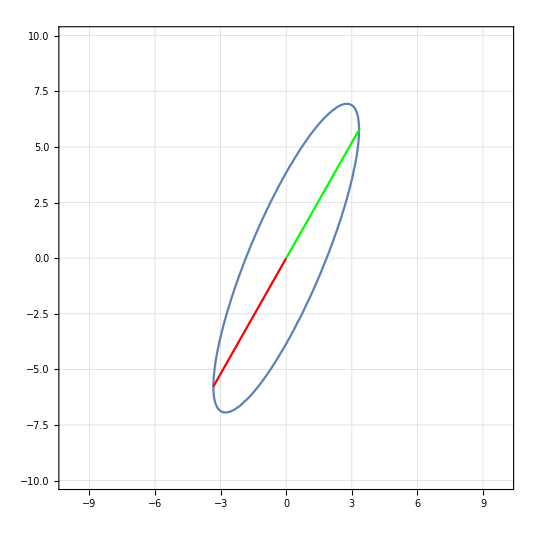

```mathematica
Show[plContourF,plF1,plF2]
```

As you can see, the forces (red and green segments) are touching the edge of the ellipse, i . e . they
are the maximum force that can be exerted in that direction given the robot configuration .

```mathematica
√(Fx1^2+Fy1^2)
```

6.66667

```mathematica
Fellipsetrasl=Fellipse/.{Fx->(Fx-EEc[[1]]),Fy->(Fy-EEc[[2]])};
```

```mathematica
plEigVecF1trasl=ListLinePlot[{point1+{EEc[[1]],EEc[[2]]},point2+{EEc[[1]],EEc[[2]]}}/.data/.ref,PlotStyle->Red];
```

```mathematica
plEigVecF2trasl=ListLinePlot[{point1+{EEc[[1]],EEc[[2]]},point3+{EEc[[1]],EEc[[2]]}}/.data/.ref,PlotStyle->Green];
```

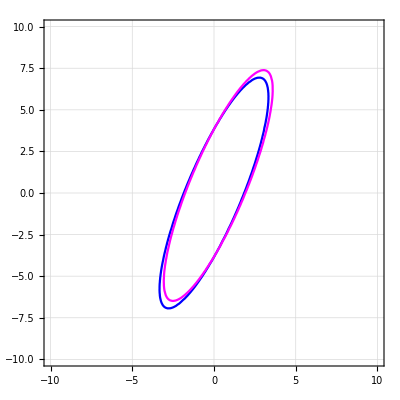

```mathematica
plContourFtrasl=ContourPlot[{(Fellipse/.data/.ref/.Kf->1)==0,(Fellipsetrasl/.data/.ref/.Kf->1)==0},
{Fx,-10,10},{Fy,-10,10},GridLines->Automatic,ContourStyle->{Blue,Magenta}]
```

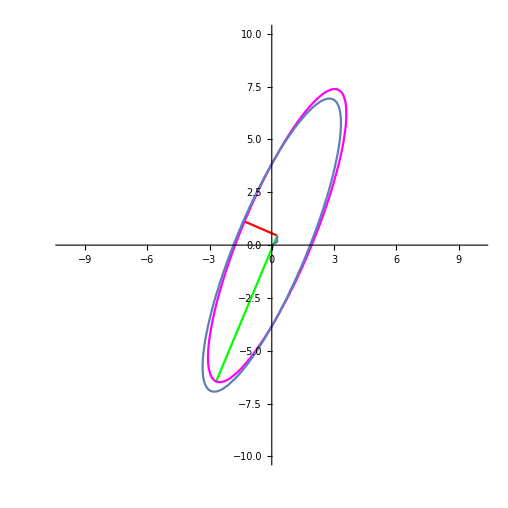

```mathematica
Show[plEigVecF1trasl,plEigVecF2trasl,plContourFtrasl,plContourF,plScara,PlotRange->{{-10,10},{-10,10}},AspectRatio->Automatic]
```

```mathematica
Fellipsetrasl/.Fx->EEc[[1]]/.Fy->EEc[[2]]/.ref/.data
```

-Kf^2

## Velocity Ellipsoid

```mathematica
AV=Transpose@Inverse@Jac.Inverse@Jac//FullSimplify;AV//MatrixForm
```

(((L1^2 Cos[θ1]^2+2 L1 L2 Cos[θ1] Cos[θ1+θ2]+2 L2^2 Cos[θ1+θ2]^2) Csc[θ2]^2)/(L1^2 L2^2) | (Csc[θ2]^2 (L1^2 Cos[θ1] Sin[θ1]+L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])))/(L1^2 L2^2)
(Csc[θ2]^2 (L1^2 Cos[θ1] Sin[θ1]+L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])))/(L1^2 L2^2) | (Csc[θ2]^2 (L1^2 Sin[θ1]^2+2 L1 L2 Sin[θ1] Sin[θ1+θ2]+2 L2^2 Sin[θ1+θ2]^2))/(L1^2 L2^2))

```mathematica
V=Transpose@{Vx,Vy};
```

```mathematica
Vellipse=Transpose@V.AV.V-Kv^2//Simplify
```

1/(L1^2 L2^2)(-Kv^2 L1^2 L2^2+L1^2 Vx^2 Cos[θ1]^2 Csc[θ2]^2+2 L1 L2 Vx^2 Cos[θ1] Cos[θ1+θ2] Csc[θ2]^2+2 L2^2 Vx^2 Cos[θ1+θ2]^2 Csc[θ2]^2+L1^2 Vy^2 Csc[θ2]^2 Sin[θ1]^2+L1^2 Vx Vy Csc[θ2]^2 Sin[2 θ1]+2 L1 L2 Vy^2 Csc[θ2]^2 Sin[θ1] Sin[θ1+θ2]+2 L2^2 Vy^2 Csc[θ2]^2 Sin[θ1+θ2]^2+2 L2^2 Vx Vy Csc[θ2]^2 Sin[2 (θ1+θ2)]+2 L1 L2 Vx Vy Csc[θ2]^2 Sin[2 θ1+θ2])

```mathematica
NumericalMatV=AV/.data/.ref
```

{{11.1111,19.245},{19.245,48.1481}}

```mathematica
EigVecV=Eigenvectors@NumericalMatV;EigVecV//MatrixForm
```

(0.391551 | 0.920156
-0.920156 | 0.391551)

```mathematica
EigValV=Eigenvalues@NumericalMatV
```

{56.3374,2.92184}

```mathematica
point1={0,0};
point2=1/(√EigValV[[1]]){Re@EigVecV[[1,1]],Re@EigVecV[[1,2]]};
```

```mathematica
point3=1/(√EigValV[[2]]){Re@EigVecV[[2,1]],Re@EigVecV[[2,2]]};
```

```mathematica
plEigVecV1=ListLinePlot[{point1,point2},PlotStyle->Red];
```

```mathematica
plEigVecV2=ListLinePlot[{point1,point3},PlotStyle->Green];
```

```mathematica
plContourV=ContourPlot[(Vellipse/.data/.ref/.Kv->1)==0,{Vx,-1,1},{Vy,-1,1},GridLines->Automatic,ContourStyle->Cyan,PlotLegends->LineLegend[{Cyan},{"Velocity"}]];
```

### Velocity Ellipsoid

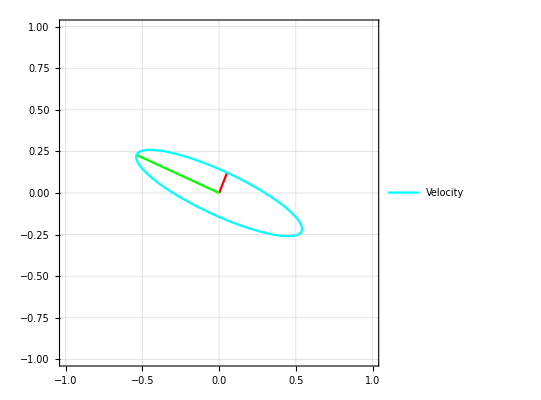

```mathematica
Show[plEigVecV1,plEigVecV2,plContourV,PlotRange->{{-1,1},{-1,1}},AspectRatio->1,GridLines->Automatic,Frame->True,Axes->False]
```

## Compliance Ellipsoid

```mathematica
Kq=k*{{1,0},{0,2}};Kq//MatrixForm
```

(k | 0
0 | 2 k)

```mathematica
Ks=Jac.Kq.Transpose@Jac//Simplify;Ks//MatrixForm
```

(k (2 L2^2 Sin[θ1+θ2]^2+(L1 Sin[θ1]+L2 Sin[θ1+θ2])^2) | -1/2 k (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2]))
-1/2 k (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])) | k (2 L2^2 Cos[θ1+θ2]^2+(L1 Cos[θ1]+L2 Cos[θ1+θ2])^2))

```mathematica
AC=Transpose[Inverse@Ks].Inverse@Ks//FullSimplify;AC//MatrixForm;
```

```mathematica
dS={dx,dy};(*generic infinitesimal displacement*)
```

```mathematica
Cellipse=Transpose@dS.AC.dS-KA^2//Simplify
```

1/(8 k^2 L1^4 L2^4)(-8 k^2 KA^2 L1^4 L2^4+dy^2 ((L1^2+3 L2^2)^2-L1^2 (L1^2+5 L2^2) Cos[2 θ1]-L2 (L1^3 Cos[2 θ1-θ2]-4 L1 (L1^2+3 L2^2) Cos[θ2]-4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4+dx^2 ((L1^2+3 L2^2)^2+L1^2 (L1^2+5 L2^2) Cos[2 θ1]+L2 (L1^3 Cos[2 θ1-θ2]+4 L1 (L1^2+3 L2^2) Cos[θ2]+4 L1^2 L2 Cos[2 θ2]+5 L1^2 L2 Cos[2 (θ1+θ2)]+9 L2^3 Cos[2 (θ1+θ2)]+3 L1^3 Cos[2 θ1+θ2]+9 L1 L2^2 Cos[2 θ1+θ2]+3 L1 L2^2 Cos[2 θ1+3 θ2])) Csc[θ2]^4+2 dx dy (L1^2+3 L2^2+2 L1 L2 Cos[θ2]) Csc[θ2]^4 (L1^2 Sin[2 θ1]+L2 (3 L2 Sin[2 (θ1+θ2)]+2 L1 Sin[2 θ1+θ2])))

```mathematica
NumericalMatC=AC/.data/.ref/.{KA->1,k->1}
```

{{123.457,356.389},{356.389,1083.68}}

```mathematica
EigVecC=Eigenvectors@NumericalMatC;EigVecC//MatrixForm
```

(0.313883 | 0.949462
-0.949462 | 0.313883)

```mathematica
EigValC=Eigenvalues@NumericalMatC
```

{1201.5,5.63801}

```mathematica
point1={0,0};
point2=1/(√(Re@EigValC[[1]]))*{EigVecC[[1,1]],EigVecC[[1,2]]};
```

```mathematica
point3=1/(√(Re@EigValC[[2]]))*{EigVecC[[2,1]],EigVecC[[2,2]]};
```

```mathematica
plEigVecC1=ListLinePlot[{point1,point2},PlotStyle->Red];
```

```mathematica
plEigVecC2=ListLinePlot[{point1,point3},PlotStyle->Green];
```

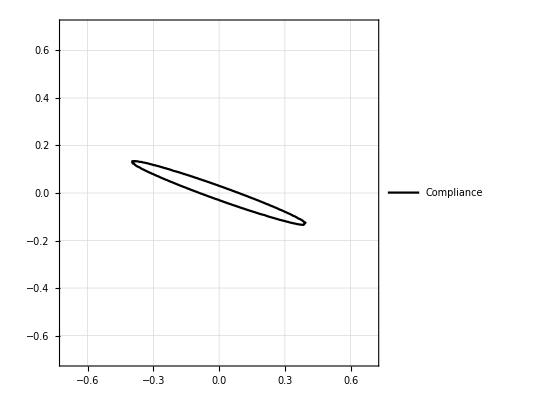

```mathematica
plContourC=ContourPlot[(Cellipse/.data/.ref/.KA->1/.k->1)==0,{dx,-0.7,0.7},{dy,-0.7,0.7},GridLines->Automatic,ContourStyle->Black,PlotLegends->LineLegend[{Black},{"Compliance"}]]
```

### Compliance Ellipsoid

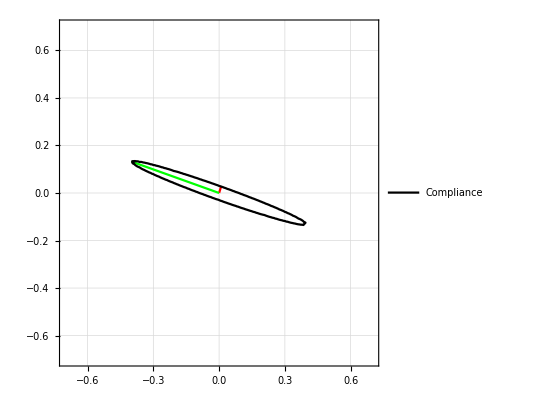

```mathematica
Show[{plEigVecC1,plEigVecC2,plContourC},PlotRange->{{-0.7,0.7},{-0.7,0.7}},GridLines->Automatic,Frame->True,Axes->False,AspectRatio->1]
```

## All ellipsoids

The compliance ellipsoid is orthogonal to the force ellipsoid only if Kq is proportional to the Identity matrix . In this case, it is not orthogonal

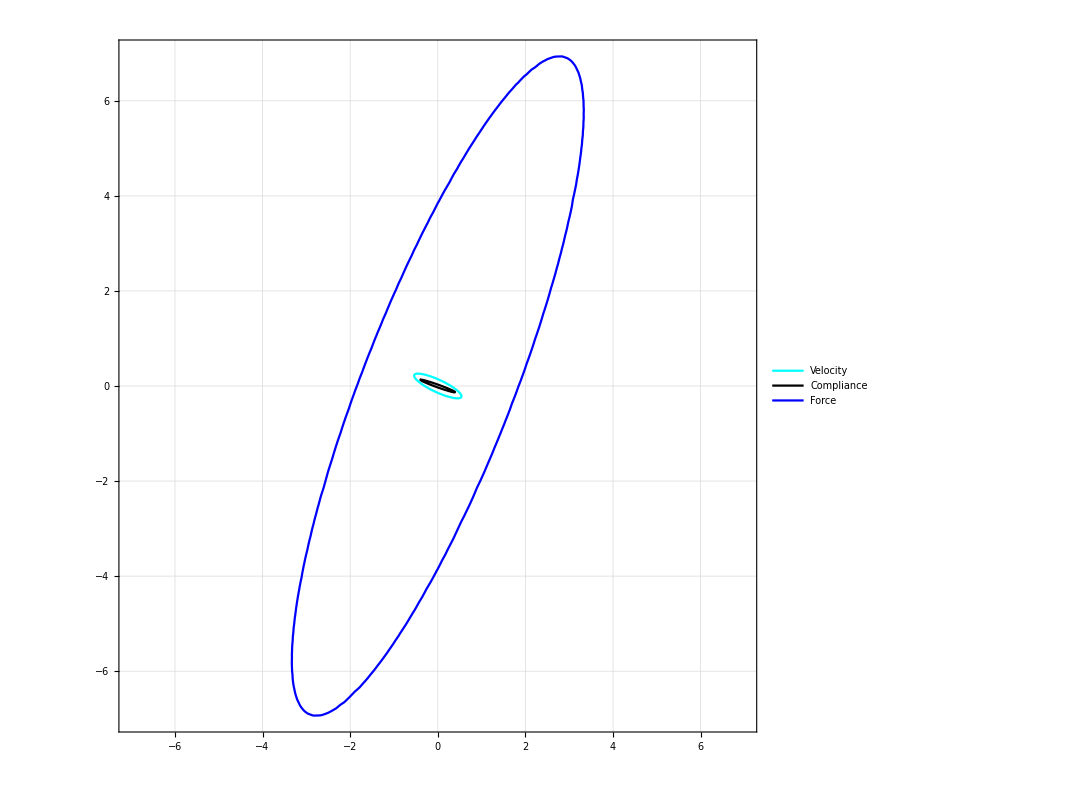

```mathematica
Show[{plContourV,plContourC,plContourF},PlotRange->{{-7,7},{-7,7}},ImageSize->800,LegendLabel->Placed[LineLegend[{Directive[Red]},{"Test"}],Bottom]]
```